Lissa de S. Campos

lissa.campos@alumni.usp.br

The goal of this notebook is to back-up the first sentence I wrote in my PhD thesis:

"---If we squeezed ourselves into grains of sand, and then crushed the entire Milky Way to fit in a
family-size pizza box, then each one of us would become a black hole that would dissipate in about
ten picoseconds. That's way longer than inflation, but still smaller than the difference of age
between your feet and your head due to Earth's gravity."

#### Becoming a tiny black hole

First, let us model a person by a sphere of unit radius and mass M_p=100kg:

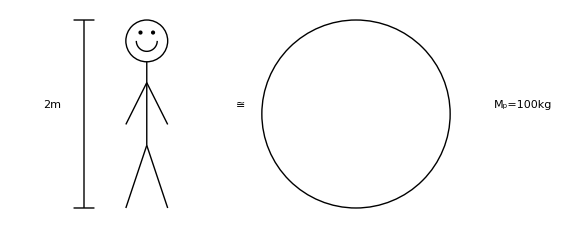

```mathematica
Graphics[{Circle[{0,0},1],Circle[{0,0},1/2,{π,2π}],Point[{-.3,.4}],Point[{.3,.4}],Line[{{0,-5},{0,-1}}],Line[{{-1,-4},{0,-2}}],Line[{{1,-4},{0,-2}}],Line[{{-1,-8},{0,-5}}],Line[{{1,-8},{0,-5}}],
Line[{{-3,1},{-3,-8}}],Line[{{-2.5,1},{-3.5,1}}],Line[{{-2.5,-8},{-3.5,-8}}],Text[Style["2m",Medium],{-4.5,-3}],Text[Style["≅",Medium],{4.5,-3}],Circle[{10,-3.5},4.5],Text[Style["M_p=100kg",Medium],{18,-3}]},ImageSize->Large]
```

For cool notation:

```mathematica
<<Notation`
Symbolize[Subscript[i_, j_]]
```

```mathematica
Subscript[M, p]=Quantity[100,"Kilograms"] ;
```

Let c be the velocity of light, G be the graviational constant , ℏ the reduced Planck constant and k the Boltzmann constant; as per ["Physical constants"](https://physics.nist.gov/cuu/Constants/index.html):

```mathematica
c=Quantity[2.99792458 10^8,"Meters"/"Seconds"] ;
G=Quantity[6.67430  10^-11,("Meters")^3/("Kilograms" ("Seconds")^2)] ; 
ℏ=Quantity[1.054571817 10^-34,("Kilograms"("Meters")^2)/("Seconds") ] ; 
Subscript[k, B]=Quantity[1.38064852 10^-23,(("Meters")^2"Kilograms")/(("Seconds")^2 "Kelvins") ];
```

["Some Simple Black Hole Thermodynamics"](https://web.stanford.edu/~oas/SI/SRGR/lib/BlackHoleThermoShort.pdf) gives us the corresponding Schwarzschild radius is given by

```mathematica
SchwarzschildRadius=(2 G Subscript[M, p])/c^2
```

1.48523×10^-25 m

and if we squeeze this person into a sphere will radius smaller than the above, then we create a cuttie tiny black hole with Hawking temperature given by

```mathematica
HawkingTemperature=(ℏ c^3)/(8 π Subscript[k, B] G Subscript[M, p])
```

1.2269×10^21 K

Wow that’s hot!  If you were a black hole you would be 10^17 times hotter than the Sun (T_(\[PermutationProduct])=5.778 10^3 K).

Alright, let us try to get an idea of how small is a person’s Schwarzschild radius. The Milky Way has a diameter of 10^21 m. If we “crushed it” to fit in a family-size pizza box, which we can model by a (1m)-side square, then we would have a new ruler where 1m correponds to the old 10^-21 m :

```mathematica
MilkyWay=Pane[ImageAdd[Import["https://upload.wikimedia.org/wikipedia/commons/8/82/Milky_Way_Galaxy.jpg"],Graphics[Disk[]]],ImageSize->250];PizzaBox=Graphics[{Inset[-Graphics-,{0,0}],{EdgeForm[Directive[Thick,Red]],Transparent,Rectangle[{-1,-1},{1,1}]}},ImageSize->40];
{x,y,z,w}={50,45.5,1.5,1};
GraphicsRow[{Graphics[{Inset[MilkyWay,{0,0}],
Line[{{x,-y},{x,y}}],Line[{{x-w,y},{x+w,y}}],Line[{{x-w,-y},{x+w,-y}}],Text[Style["10^21m",Medium],{x+5z,0}],Text[Style["↦",Medium],{x+12z,0}],
Line[{{x+16z,-y/10},{x+16z,y/10}}],Line[{{x+16z-w,y/10},{x+16z+w,y/10}}],Line[{{x+16z-w,-y/10},{x+16z+w,-y/10}}],
Text[Style["1m",Medium],{x+19z,0}]}],PizzaBox}]
```

-Graphics-

Squeezing the person inside a grain of sand:

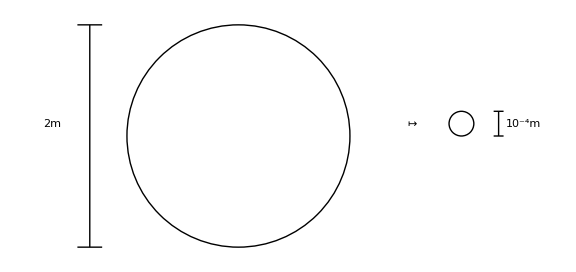

```mathematica
Graphics[{
Line[{{-3,1},{-3,-8}}],Line[{{-2.5,1},{-3.5,1}}],Line[{{-2.5,-8},{-3.5,-8}}],Text[Style["2m",Medium],{-4.5,-3}],Circle[{3,-3.5},4.5],Text[Style["↦",Medium],{10,-3}],Circle[{12,-3},.5],
Line[{{13.5,-3.5},{13.5,-2.5}}],Line[{{13.3,-3.5},{13.7,-3.5}}],Line[{{13.3,-2.5},{13.7,-2.5}}],
Text[Style["10^-4m",Medium],{14.5,-3}]},ImageSize->Large]
```

A grain of sand (previously with a diameter of about 10^-4 m) has  around 10^-25 m  in our new scale.

That is a whole lot of squeezing to make a person become a black hole! In fact, we have that the density of the squeezed person is 10^75 times the density of the person:

```mathematica
rPerson=Quantity[1,"Meters"];
rSqueezedPerson=Quantity[10^-25,"Meters"];
(*
DensityPerson=M/(4/3 π rPerson^3); 
DensitySqueezedPerson=M/(4/3 π rSqueezedPerson^3);
DensitySqueezedPerson/DensityPerson==rPerson^3/rSqueezedPerson^3
*)
ScientificForm@N[rPerson^3/rSqueezedPerson^3]
```

1.×10^75

#### Dissipating

Suppose we get it done. After all that work to create a cuttie tiny black hole, it will start evaporating. Its life-time would be of around

```mathematica
EvaporationTime=(5120π G^2 Subscript[M, p]^3)/(ℏ c^4)
```

8.41148×10^-11 s

Could we even see this black hole? Is 10^-10 s a scale currently detectable in laboratories? To what element would this decay time correspond to?

In one second, a caesium atom resonates 9192631770 times (see e.g. ["The most accurate clock of all time"](https://www.newscientist.com/article/dn7397-the-most-accurate-clock-of-all-time/#:~:text=Today's%20caesium%20clocks%20can%20measure,in%20about%2030%20million%20years.&text=That%20is%20why%20people%20went,with%2010%2C000%20oscillations%20per%20second.)). That is, it resonates once every 10^-10 s:

```mathematica
CaesiumPeriod=Quantity[ScientificForm@N[1/9192631770],"Seconds"]
```

1.08783×10^-10 s

Thus, it kinda feels like a palpable time, no? At least for caesium it is.

NB: I wrote in my thesis  “10 pico-seconds”  and not “100 pico-seconds”, but that’s ok! I had done the computation handwavingly in orders of magnitude, not with the precise constants and all. In this estimation an order of 10 doesn’t matter much.

#### How much could Earth’s gravity affect us?

It is known that we must take General Relativity into account when setting up our satellites around Earth and synchronizing their clocks in order to use GPS, for example. Now, suppose a person passes her whole life standing up, with a clock attached to her feet, and another one to her head. After 30 years how dissyncronized would these clocks be? What order of magnitude would you expect? Did you know that the  ["Earth's core is two-and-a-half years younger than its crust"](https://www.newscientist.com/article/2085599-earths-core-is-two-and-a-half-years-younger-than-its-crust/#:~:text=Physicists%20have%20calculated%20that%20the,which%20you%20experience%20time%20passing.)?

Let us adapt what was done for the Earth’s core and surface, in the paper “["The young centre of the Earth"](https://iopscience.iop.org/article/10.1088/0143-0807/37/3/035602)”,  to compute the time difference for the person’s feet and head. Let R_♁ and M_♁ be the Earth’s radius and mass respectively, and let g be the corresponding gravitational acceleration. Earth’s gravitational potential at r>=R_♁ is given by

Φ[r_]:=- (G M_♁)/r

Suppose the person’s height is h_p=2m. The potential difference between the person’s feet at r=R_♁ and the person’s head at r=R_♁+h reads

ΔΦ_p=Φ[R_♁+h]-Φ[R_♁]= G M_♁ h_p/(R_♁(R_♁+h_p))~G M_♁ h_p/(R_♁)^2=g h_p

If t_p is the time the person has been standing-up, according to one of her clocks, then the time difference due to ΔΦ_p is given by ΔΦ_p/c^2 t_p :

```mathematica
g=Quantity[9.80665,("Meters")/("Seconds")^2];
Subscript[h, p]=Quantity[2,"Meters"];
Subscript[t, p]=Quantity[30,"Years"];
AgeDifference=Quantity[(g Subscript[h, p])/c^2 Subscript[t, p],"Seconds"]
```

2.06461×10^-7 s^2

NB: after I had done the somewhat rough estimate above, I saw tha NIST estimates that the time difference is  of the order of  μs for an eighty years old that had lived a “normal” life (not upside-down most of time). That is, the estimate above is not bad at all! One can read about it here:  ["NIST Clock Experiment Demonstrates That Your Head is Older Than Your Feet"](https://www.nist.gov/news-events/news/2010/09/nist-clock-experiment-demonstrates-your-head-older-your-feet)

AgeDifference is one thousend times larger than EvaporationTime!

```mathematica
ScientificForm@N[AgeDifference/EvaporationTime]
```

2.45451×10^3 s

AgeDifference is probably way larger than one would expect, and EvaporationTime, much smaller. What kind of process would give even smaller time scales? There are many answers to that. Let us choose one: inflation. From Wikipedia we get some info:

```mathematica
TextSentences[WikipediaData["Inflation (cosmology)"]][[;;2]]
```

{In physical cosmology, cosmic inflation, cosmological inflation, or just inflation, is a theory of exponential expansion of space in the early universe.,The inflationary epoch lasted from 10−36 seconds after the conjectured Big Bang singularity to some time between 10−33 and 10−32 seconds after the singularity.}

That is:

```mathematica
InflationDuration=Quantity[10^-33-10^-36,"Seconds"];
ScientificForm@N[InflationDuration]
```

9.99×10^-34 s

Therefore, EvaporationTime is 10^23 times larger than InflationDuration! Which is 100 times larger than the size of the Milky Way in meters...

```mathematica
ScientificForm@N[EvaporationTime/InflationDuration]
```

8.4199×10^22